## Inapplicability of the χ tests

Although this appears obvious, let us construct an explicit example that shows that the χ tests are not appropriate to test the posterior distributions. The example below is completely analytic, and I’ve chosen parameters to mimic the issue we’ve seen.

```mathematica
(* Set up a probability distribution *)

$Assumptions = {σ>0};
prob[x_, α_, σ_]:= α/(√(2π))Exp[-x^2/2] + (1-α)/(2σ)Exp[-Abs[x]/σ];
```

```mathematica
(* Analytic, but get Mathematica to check answer *)
```

```mathematica
Integrate[x^2 prob[x,α, σ],{x,-Infinity,Infinity}]
```

α+2 σ^2-2 α σ^2

```mathematica
sig[α_,σ_] := Sqrt[α+2 σ^2-2 α σ^2];
```

```mathematica
(* Here are some trivial choices --- this closely mimics the issue we are seeing *)
```

```mathematica
sig[0.8, 1.7]
```

1.39857

```mathematica
(* Calculate the χ distribution *)
```

```mathematica
pchi[xt_, α_, σ_]:= prob[xt*sig[α,σ],α,σ] sig[α,σ];
```

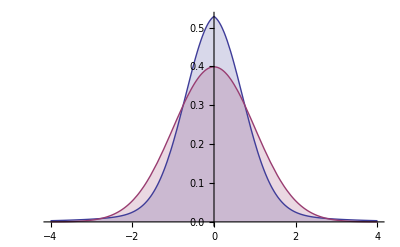

```mathematica
Plot[{pchi[x,0.8,1.7],prob[x,1,1]},{x,-4,4}, Filling->Axis]
```

## Sensitivity of the KS test

Using the above distribution, we test to see if the KS test could have correctly ruled out the unit normal hypothesis for different numbers of samples.

```mathematica
𝒟 = ProbabilityDistribution[pchi[x, 0.8,1.7], {x,-∞, ∞}];
```

```mathematica
(* A random sampling from the distribution *)
```

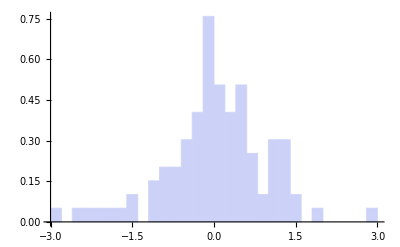

```mathematica
Histogram[RandomVariate[𝒟, 100], {-3,3,0.2}, "PDF"]
```

```mathematica
(* Generate three sets of data, with 100, 160, 600 elements *)
```

```mathematica
data100 =RandomVariate[𝒟,{10^3,100}];
data160 = RandomVariate[𝒟, {10^3, 160}];
data600 = RandomVariate[𝒟, {10^3, 600}];
```

```mathematica
(* Generate p-value distributions for each of these cases, comparing to the unit normal *)
```

```mathematica
pvals100 = KolmogorovSmirnovTest[#, NormalDistribution[], "PValue"] & /@ data100;
pvals160 = KolmogorovSmirnovTest[#, NormalDistribution[], "PValue"] & /@ data160;
pvals600 = KolmogorovSmirnovTest[#, NormalDistribution[], "PValue"] & /@ data600;
```

```mathematica
(* Now plot the cumulative distribution in each of these cases *)
```

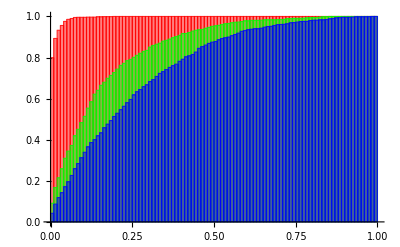

```mathematica
Histogram[{pvals600, pvals160, pvals100},{0,1,0.01}, "CDF", ChartStyle->{Red, Green, Blue}]
```

The Anderson-Darling test is a similar comparison to the cumulative distribution function, except it weights points in the tails more...

```mathematica
(* Overwrite pvals with the tests from the Anderson-Darling tests *)
```

```mathematica
p1vals100 =AndersonDarlingTest[#, NormalDistribution[], "PValue"] & /@ data100;
p1vals160 = AndersonDarlingTest[#, NormalDistribution[], "PValue"] & /@ data160;
p1vals600 = AndersonDarlingTest[#, NormalDistribution[], "PValue"] & /@ data600;
```

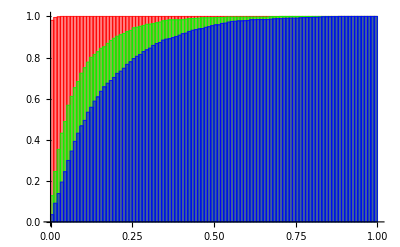

```mathematica
Histogram[{p1vals600, p1vals160, p1vals100},{0,1,0.01}, "CDF", ChartStyle->{Red, Green, Blue}]
```

```mathematica
(* Compare the 100 object cases *)
```

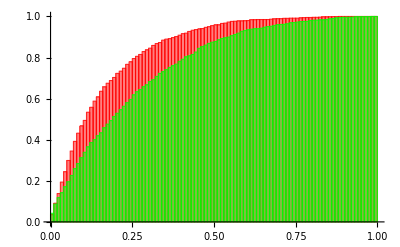

```mathematica
Histogram[{p1vals100, pvals100},{0,1,0.01}, "CDF", ChartStyle->{Red, Green}]
```